## A366719: Smallest prime dividing 12^n + 1.

### MATHEMATICA PROGRAM:

```mathematica
Table[FactorInteger[12^n+1][[1,1]],{n,0,69}] (* Paul F.Marrero Romero, Oct 25 2023 *)
```

{2,13,5,7,89,13,5,13,17,7,5,13,89,13,5,7,153953,13,5,13,41,7,5,13,17,13,5,7,89,13,5,13,769,7,5,13,89,13,5,7,17,13,5,13,89,7,5,13,7489,13,5,7,89,13,5,13,17,7,5,13,41,13,5,7,36097,13,5,13,89,7}

### Formula:

a(n) = A020639(A178248(n)).  - Paul F. Marrero Romero, Oct 25 2023

### Plot section:

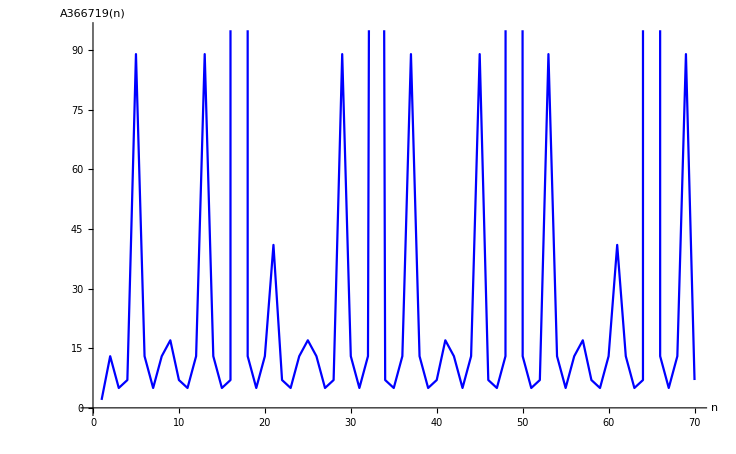

```mathematica
ListPlot[Table[FactorInteger[12^n+1][[1,1]],{n,0,69}], Joined->True, PlotStyle->Blue, AxesLabel->{"n", "A366719(n)"}, LabelStyle->Directive [Black, Bold]]
```

### References:

Sean A. Irvine, Smallest prime dividing 12^n + 1, Entry A366719 in The On-Line Encyclopedia of Integer Sequences, https://oeis.org/A366719